```mathematica
a=2;b=3;c=4;
Show[RegionPlot3D[x/a+y/b+z/c<=1&&x>=0&&y>=0&&z>=0,{x,0,2},{y,0,3},{z,0,4},PlotTheme->"Minimal",ColorFunction->"Rainbow"],
ContourPlot3D[z==1.0,{x,0,2},{y,0,3},{z,0,4},ContourStyle->Directive[Opacity[0.5],Red]]
]
```

-Graphics3D-

```mathematica
Clear[a,b,c]
Integrate[Integrate[Integrate[y,{y,0,b(1-x/a-z/c)}],{x,0,a(1-z/c)}],{z,0,c}]
```

1/24 a b^2 c

```mathematica
Show[RegionPlot3D[z>=0&&x^2+y^2<=2x&&z<=x^2+y^2,{x,0,2},{y,-1.5,1.5},{z,0,2},PlotTheme->"Detailed",ColorFunction->"Rainbow"]
]
```

-Graphics3D-

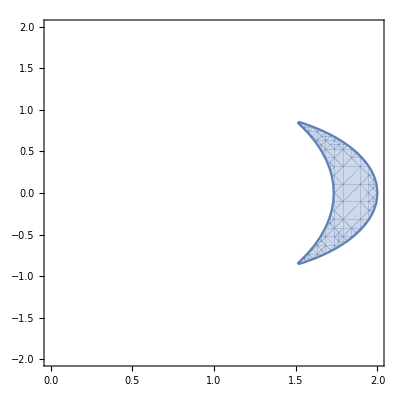

```mathematica
RegionPlot[x^2+y^2<=2x&&3<=x^2+y^2,{x,0,2},{y,-2,2}]
```

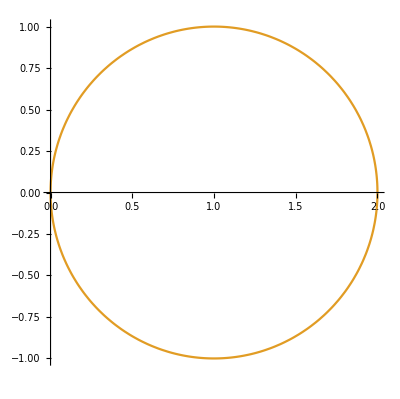

```mathematica
u=0;
PolarPlot[{Sqrt[u],2Cos[t]},{t,-ArcCos[Sqrt[u]/2],+ArcCos[Sqrt[u]/2]}]
```

```mathematica
Clear[r,u,t]
Integrate[Integrate[Integrate[u r,{r,Sqrt[u],2Cos[t]}],{t,-ArcCos[Sqrt[u]/2],+ArcCos[Sqrt[u]/2]}],{u,0,4}]
```

(5 π)/3

```mathematica
Volume[ImplicitRegion[z>=0&&x^2+y^2<=2x&&z<=x^2+y^2,{x,y,z}]]
```

(3 π)/2

```mathematica
2Pi/(3Pi/2)
```

4/3

```mathematica
ν[t_]=(1+β)^t n0+δn/β((1+β)^t-1);
Solve[ν[τ]==n&&ν[T]==N,{T,δn}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{T→Log[(n-N+N (1+β)^τ-n0 (1+β)^τ)/(n-n0)]/Log[1+β],δn→-(β (-n+n0 (1+β)^τ))/(-1+(1+β)^τ)}}

```mathematica
Log[(500-1000+1000 (1+0.04)^3-300 (1+0.04)^3)/(500-300)]/Log[1+0.04]
```

9.24446

```mathematica
((3.0/7)^20-(3.0/7)^50)/(1-(3.0/7)^50)
```

4.36983×10^-8

```mathematica
Table[((3.0/7)^t-(3.0/7)^50)/(1-(3.0/7)^50),{t,0,50}]
```

{1.,0.428571,0.183673,0.0787172,0.0337359,0.0144583,0.0061964,0.0026556,0.00113811,0.000487763,0.000209041,0.0000895891,0.0000383953,0.0000164551,7.05221×10^-6,3.02237×10^-6,1.2953×10^-6,5.5513×10^-7,2.37913×10^-7,1.01963×10^-7,4.36983×10^-8,1.87278×10^-8,8.02621×10^-9,3.43981×10^-9,1.4742×10^-9,6.31801×10^-10,2.70772×10^-10,1.16045×10^-10,4.97336×10^-11,2.13144×10^-11,9.13474×10^-12,3.91489×10^-12,1.67781×10^-12,7.19061×10^-13,3.08169×10^-13,1.32072×10^-13,5.66021×10^-14,2.42578×10^-14,1.0396×10^-14,4.45519×10^-15,1.90914×10^-15,8.17975×10^-16,3.50333×10^-16,1.49914×10^-16,6.40209×10^-17,2.72094×10^-17,1.14331×10^-17,4.6718×10^-18,1.7741×10^-18,5.3223×10^-19,0.}

```mathematica
WolframAlpha["step-by-step solve B[t+1]==(1+r) B[t]+b if B[0]=B0"]
```

WolframAlphaQueryResults

```mathematica
Table[1.04^k*300+52.07/0.04(1.04^k-1),{k,0,11}]
```

{300.,364.07,430.703,500.001,572.071,647.024,724.975,806.044,890.355,978.04,1069.23,1164.07}

```mathematica
Show[
ParametricPlot3D[{t,t^2/Sqrt[2],t^3/3},{t,0,Sqrt[2]},PlotTheme->"Business"],
ListPointPlot3D[{{0,0,0},{Sqrt[2],Sqrt[2],(2Sqrt[2])/3}}->{"A","B"}]
]
```

-Graphics3D-

```mathematica
Show[
ContourPlot3D[{x^2+y^2+z^2==4},{x,-2,2},{y,-2,2},{z,-2,2},PlotTheme->"Business"],
ParametricPlot3D[{Sqrt[2]Sin[t],Sqrt[2]Sin[t],2Cos[t]},{t,0,Pi/4},PlotStyle->Red],
ListPointPlot3D[{{0,0,2},{1,1,Sqrt[2]}}->{"A","B"},PlotStyle->Red]
]
```

-Graphics3D-

```mathematica
x=r Sin(t)
```